## grupa 1

#### Zad. 1

3-4 x+x^2

{{x→1},{x→3}}

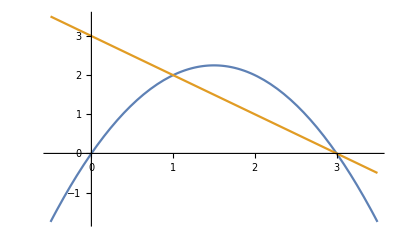

4/3

```mathematica
(x-1)(x-3)//Expand
y1=3x-x^2;
y2=3-x;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-0.5,3.5}]
Integrate[y1-y2,{x,1,3}]
```

#### Zad. 2

```mathematica
A1={{1,2,3},{3,2,1},{2,3,1}};
Det[A1]
X1={{2},{1},{-3}};
B1=A1.X1
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

12

{{-5},{5},{4}}

{{x→2,y→1,z→-3}}

#### Zad. 3

```mathematica
A1={{1,2,2,1},{2,1,1,2},{2,2,1,1},{1,1,-2,2}};
Det[A1]
X1={{0},{-2},{3},{0}};
B1=A1.X1
Solve[A1.{{x},{y},{z},{t}}==B1,{x,y,z,t}]
```

12

{{2},{1},{-1},{-8}}

{{x→0,y→-2,z→3,t→0}}

## grupa I1

#### Zad. 1

```mathematica
y=1/x^2;
π Integrate[y,{x,1,3}]
```

(2 π)/3

#### Zad. 2

```mathematica
A1={{2,-1,1},{1,3,-2},{-3,2,1}};
X1={{0},{1},{2}};
B1=A1.X1
Clear[y];
Solve[A1.{{x},{y},{z}}==B1,{x,y,z}]
```

{{1},{-1},{4}}

{{x→0,y→1,z→2}}

#### Zad. 3

```mathematica
A1={{1,2,3,1},{1,1,-2,3},{3,1,1,2},{-2,3,1,1}};
Det[A1]
X1={{0},{0},{-1},{0}};
B1=A1.X1
Solve[A1.{{x},{y},{z},{t}}==B1,{x,y,z,t}]
```

19

{{-3},{2},{-1},{-1}}

{{x→0,y→0,z→-1,t→0}}